# Shrink it, baby!

#### options settings

```mathematica
SetDirectory["/home/julian/mathematica/CVL"];
ClearSystemCache[];
Needs["Splines`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["ErrorBarPlots`"];
Directory[]
```

/home/julian/mathematica/CVL

```mathematica
SetOptions[Interpolation, InterpolationOrder -> 4, PeriodicInterpolation -> True];
Options[Interpolation]
```

{InterpolationOrder→4,PeriodicInterpolation→True}

```mathematica
SetOptions[NIntegrate, MaxRecursion -> 20];
Options[NIntegrate, MaxRecursion]
```

{MaxRecursion→20}

```mathematica
SetOptions[NDSolve`FiniteDifferenceDerivative, DifferenceOrder -> 6, PeriodicInterpolation -> True];
Options[NDSolve`FiniteDifferenceDerivative]
```

{DifferenceOrder→6,PeriodicInterpolation→True}

```mathematica
SetOptions[NDSolve, MaxSteps -> 15000];
Options[NDSolve, {MaxSteps, InterpolationOrder}]
```

{MaxSteps→15000,InterpolationOrder→Automatic}

```mathematica
SetOptions[NDSolve`ProcessEquations, MaxSteps -> 15000];
Options[NDSolve`ProcessEquations, MaxSteps]
```

{MaxSteps→15000}

```mathematica
Clear[labfontsize,labfontthickness,plotlabsize];
labfontsize=28;
labfontthickness=Plain;
plotlabsize=24;
```

## ensemble of initial curves

### functions

#### curve generator

```mathematica
Clear[pcg,rpcg];
pcg[num_,xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9];

Subscript[curve, num][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);

Show[
ListPlot[10Sqrt[2π/area]Table[xy[[i]]-centroid,{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],AspectRatio->Full],
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi}]]

];


rpcg[num_,xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid,curve},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9];

Subscript[curve, num][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[spline[2+(n)i/100],{i,0,100}]],
ParametricPlot[spline[u],{u,2,2+n}]],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}]],
ParametricPlot[initialcurve[u],{u,0,2Pi}],
Graphics[{Green,PointSize[Medium],Point[centroid]}]],
Show[
ListPlot[10Sqrt[2π/area]Table[xy[[i]]-centroid,{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],AspectRatio->Full],
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi}]]
}}]
];
]
```

### ensemble

#### initial curves

```mathematica
pcg[0,{{0,4},{4,0},{0,-4},{-4,0}}];
pcg[1,{{0,4},{4,0},{0,-4},{0,-1},{-1,2},{-2,1},{-1,-1},{-3,-1}}];
pcg[2,{{0,4},{3,3},{2,1},{0,2},{0,0},{4,-1},{0,-4},{-4,0}}];
pcg[3,{{-1,3},{0,3},{1,1},{4,0},{2,-2},{1,-1},{0,-1},{-1,-2},{-4,0},{-3,1},{-3/2,0}}];
pcg[4,{{0,2},{0,4},{2,2},{4,0},{0,-4},{0,-1},{2,-1},{2,0}}];
pcg[5,{{0,1},{2,2},{2,0},{-2,0},{0,-3},{-1,-4},{-2,-2},{-4,0},{-2,4}}];
pcg[6,{{0,1},{2,2},{2,0},{0,-3},{-1,-4},{-2,-2},{-4,-2},{-4,0},{-2,-1}}];
pcg[7,{{0,-1},{2,0},{3,0},{2,-2},{3,-4},{0,-4},{-1,-3},{-4,-2},{-3,0},{-2,1}}];
pcg[8,{{0,1},{4,4},{4,1},{2,0},{3,-2},{0,-3},{-2,-3},{-4,0},{-1,4}}];
pcg[9,{{1,4},{2,2},{4,1},{2,0},{-2,0},{1,-4},{-3,-5},{-4,-8},{-6,-6},{-4,-4},{-4,1},{-2,2}}];
pcg[10,{{-1/4,1/10},{3,2},{2,-1},{0,-1/8},{-4,-1},{-4,4}}];
pcg[11,{{-8,4},{-4,6},{0,8},{2,6},{-5,4},{-4,3},{4,4},{5,0},{2,0},{0,-4},{-2,-3},{1,1},{0,2},{-4,0}}];
pcg[12,{{-3,5},{1,2},{3,3},{4,0},{-2,3},{-3,2},{-5/4,1/2},{-2,-3/2},{-3/2,-2},{0,-2},{0,-4},{-3,-2},{-5,-1},{-5,0},{-4,2}}];
```

#### ensemble plot

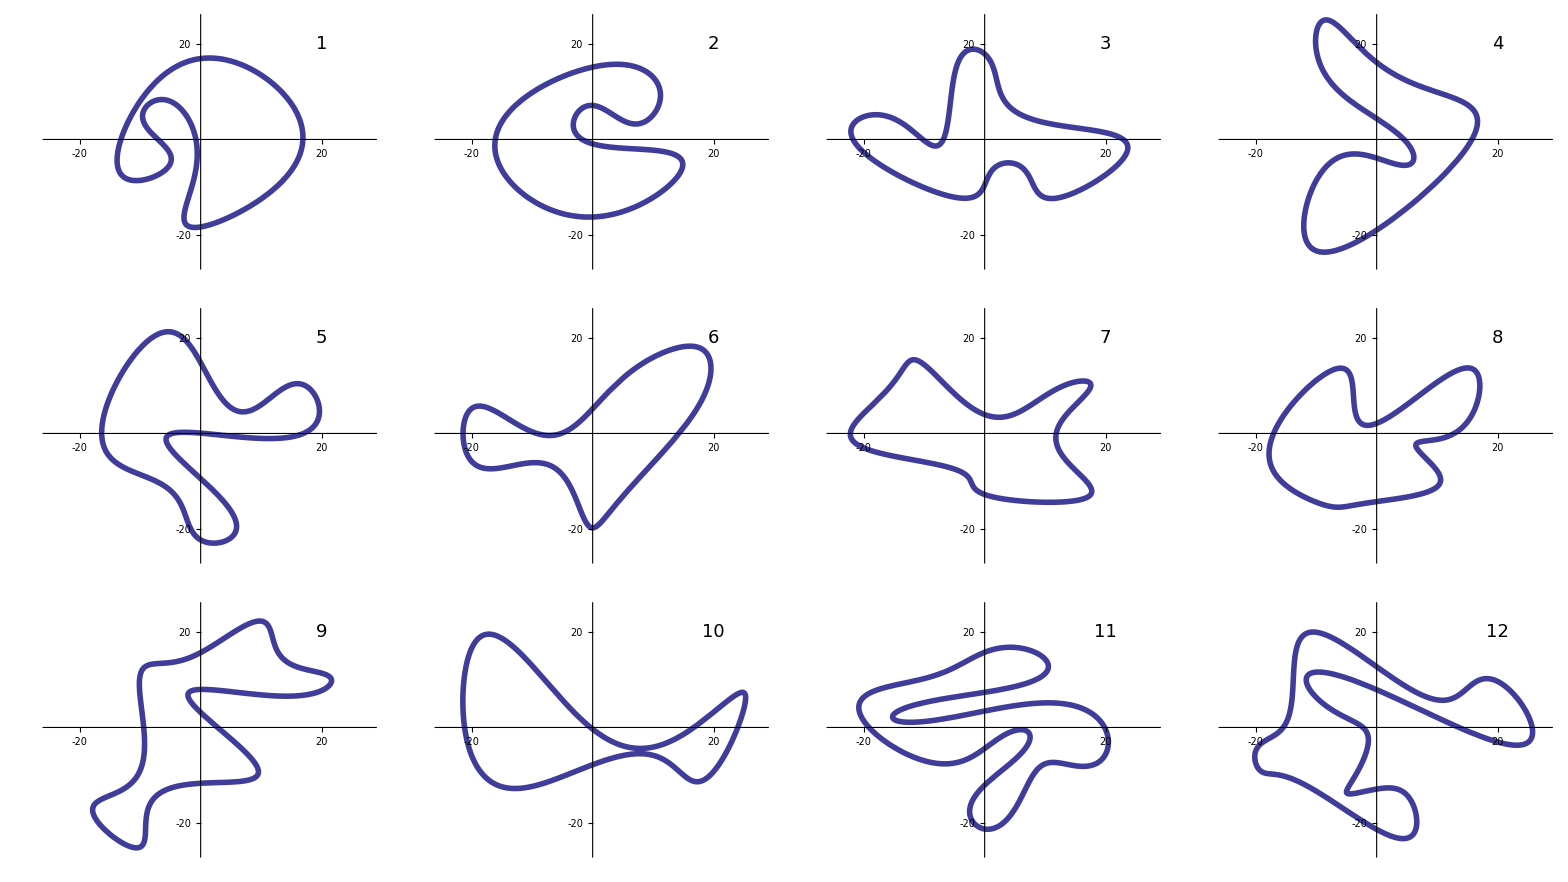
y | -Graphics-
 | x

```mathematica
Block[{iniplots},
iniplots=
Framed@Labeled[
TableForm[
Block[{columns=4,rows=3,n,i,j},
n=columns(i-1)+j;
Table[
ParametricPlot[Subscript[curve, n][u],{u,0,2π},
PlotStyle->Thickness[.01],
PlotRange->{{-25,28},{-26,25}},
Epilog->Text[Style[n,18],{20,20}],
Ticks->{{-20,20},{-20,20}},
AxesStyle->Arrowheads[Automatic]
],{i,1,rows},{j,1,columns}
]
]
],{Style[y,labfontsize,labfontthickness],Style[x,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];
Export["plots/0InitialCurves.eps",iniplots];
Export["/home/julian/latex/thesis/0InitialCurves.eps",iniplots];
iniplots
]
```

## curve evolution & fits

### functions

#### plotting

```mathematica
Clear[lineplot3d,evoplot3d,evocenplot3d];

lineplot3d[sol_List,scale_,opts___]:=
Module[{plots,n,t1,t2},

n=Length[sol]/2-1;
{t1,t2}=First[First[sol][[2]]][[1]];
If[t2≤99&&t2>1,t2=t2-1];

plots=Table[{Subscript[x, i][t]/.sol[[i+1]],Subscript[y, i][t]/.sol[[i+n+2]],t/scale},{i,0,n}
];
ParametricPlot3D[plots//Evaluate,{t,t1,t2},AspectRatio->1,AxesStyle->Arrowheads[Automatic],PerformanceGoal->"Speed",opts]
];

evoplot3d[num_Integer,scale_,opts___]:=
Module[{sol,n,curplot,lineplots},
sol=Subscript[solution, num];
n=Length[sol];

curplot=ParametricPlot3D[
{Flatten@{Subscript[curve, num][u],0},{0,0,100/scale}},
{u,0,2π},PlotRange->All,PlotStyle->{{Black,Thickness[.01]},{White,Thin}},PerformanceGoal->"Speed",opts];
lineplots=Table[lineplot3d[sol[[i]],scale,PlotStyle->{{RGBColor[0,0,.4],Thin}}],{i,1,n}];

Show[curplot,lineplots]
];

evocenplot3d[num_,scale_:3,opts___]:=
Show[
evoplot3d[num,scale,opts],
ParametricPlot3D[Flatten@{Subscript[com, num][t],t},{t,0,99.7/scale},PlotRange->Full,PlotStyle->{Thickness[.01],Red}]
];
```

#### n points on curve

```mathematica
Clear[curgrdpts];

curgrdpts[num_Integer,n_Integer:150]:=
Block[{pts},
pts=Thread[Subscript[curve, num][2π Range[0,n]/n]];
Table[{2π i/n,pts[[i+1]]},{i,0,n}]
];
```

#### process equation

```mathematica
Clear[proequ];

proequ[t0_:0,icpts_List]:=
Module[{n,grdpts,ugrid,X,Y,xu,xuu,yu,yuu,v,xeqns,yeqns,ic,xic,yic},

n=Length[icpts]-1;
grdpts=Range[0,n];
ugrid=icpts[[All,1]];

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Sqrt[xu^2+yu^2];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

ic=Flatten@Table[Thread[{Subscript[x, i][t0],Subscript[y, i][t0]}==icpts[[i+1,2]]],{i,0,n}];

First[
NDSolve`ProcessEquations[
Join[xeqns,yeqns,ic],
Join[Thread[Subscript[x, grdpts]],Thread[Subscript[y, grdpts]]],
t]
]

];
```

#### length & area

```mathematica
Clear[length,area];

length[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]]

];

area[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[fddf[X]Y -fddf[Y]X,1]]/2

];
```

#### pretest

```mathematica
Clear[pretest];
pretest[state_NDSolve`StateData]:=
Block[{sta,t,sol,n,grid,X,Y,fddf},
sta=state;
t=First[state@"CurrentTime"];
NDSolve`Iterate[sta,t];
sol=NDSolve`ProcessSolutions[sta];

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

1000Abs[
Total[Drop[Y  fddf[X] -X  fddf[Y],1]]/2+2π t -200π
]

]
```

#### error test

```mathematica
error[sol_List,t_]:=
Block[{t1,t2,n,grid,X1,Y1,X,Y,fddf},

{t1,t2}=First[First[sol][[2]]][[1]];
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;

1000Abs[
(Total[Drop[fddf[X]Y -fddf[Y]X,1]]-Total[Drop[fddf[X1]Y1 -fddf[Y1]X1,1]])/2
+2π( t-t1 )]

];
```

#### (cutfit)

Not used. Doesn' t work properly.

```mathematica
Clear[cut];

cut[sol_List]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,l1,l2,l,i,j,d,
newdist,nnew,newX,newY,newgrid},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=1Min@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];
Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
Prepend[newgrid,{0,Last[newgrid][[2]]}]

]
```

#### fit

```mathematica
Clear[fit];

fit[sol_List]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,l1,l2,l,i,j,d,
newdist,nnew,newX,newY,newgrid,
xmdp,ymdp,order,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,fc},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=1Min@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];
;
Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
newgrid=Prepend[newgrid,{0,Last[newgrid][[2]]}];

xmdp=Table[{newgrid[[i,1]],newgrid[[i,2,1]]},{i,1,nnew+1}];
ymdp=Table[{newgrid[[i,1]],newgrid[[i,2,2]]},{i,1,nnew+1}];

order=16-IntegerPart[t2/8];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

fc[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};
Print["Fit at time ",t2," Deviation in curve length: ",100(NIntegrate[Sqrt[Evaluate[(D[fc[u], u]).(D[fc[u], u])]],{u,0,2π}]-l2)/l2,
"%"
];

Table[{2π i/ nnew,fc[2π i/nnew]},{i,0,nnew}]
]
```

#### evolution

```mathematica
Clear[evolution];

evolution[num_Integer,n_Integer:150]:=
Module[{grid,state,dt,sol,er,t,tfinal},
Subscript[solution, num]={};

grid=curgrdpts[num,n];
state=proequ[0,grid];
er=pretest[state];
If[er>.5,Return[Print["Pretest failed at t=",0," the error was ",er," (wild curve)"]]];

For[t=0,t<100,t++,
NDSolve`Iterate[state,t];
sol=NDSolve`ProcessSolutions[state];
er=error[sol,t];
If[er>2,
Subscript[solution, num]=Append[Subscript[solution, num],sol];
Block[{t1,t2,newgrid,newstate,newsol,newer},
{t1,t2}=First[First[sol][[2]]][[1]];
newgrid=fit[sol];
newstate=proequ[t2-1,newgrid];
NDSolve`Iterate[newstate,t2];
newsol=NDSolve`ProcessSolutions[newstate];
newer=error[newsol,t2];
If[newer≥ 2,
Print["Error after iteration of fitted state. The error was ",newer, "(",er,") at time ",t2,"(",t2-1,")"];
Abort[];
];
state=newstate;
];
];
];
tfinal=area[sol,99]/(2π)+99;
NDSolve`Iterate[state,tfinal];
sol=NDSolve`ProcessSolutions[state];

Subscript[solution, num]=Append[Subscript[solution, num],sol];
]
```

#### selector (input: solutions & time, output: coords {x,y} according time), picker

```mathematica
Clear[selector,picker];

selector[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
grid=Range[0,Length[sol[[i]]]/2 -1];
X=Through[Thread[Subscript[x, grid]][t]]/.sol[[i]];
Y=Through[Thread[Subscript[y, grid]][t]]/.sol[[i]];
{X,Y}
];

picker[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
i
]
```

#### fufu : multifu

```mathematica
Clear[fmulti];

fmulti[num_Integer,t_]:=
Module[{sol=Subscript[solution, num],X,Y,n,fddf,v,l,len,are},

{X,Y}=selector[sol,t];
n=Length@X-1;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];
v=Sqrt[fddf[X]^2 +fddf[Y]^2];
l=Total[Drop[v,1]];

{
(*{length,area,length^2/area,centroid,}*)
len=Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]],
are=Total[Drop[fddf[X]Y -fddf[Y]X,1]]/2,
len^2/are,
{Total[Drop[X v,1] ],Total[Drop[Y v,1]]}/l
}

]
```

#### fufufits

```mathematica
Clear[fullfits];

fullfits[num_Integer,fitpts_:100,isoorder_:16,aorder_:4,comorder_:12,isoerexp_:2,areaerexp_:3]:=
Module[{tmax=99.9,tab,t,area},

tab=Table[Flatten[{tmax i/fitpts,fmulti[num,tmax i/fitpts]}],{i,0,fitpts}];

Subscript[iso, num][t_]=Fit[tab[[All,{1,4}]],Thread[t^Range[0,isoorder]],t];
Subscript[l, num][t_]=Sqrt[Subscript[iso, num][t] (200 π-2 π t)];
area[num,t_]=Fit[tab[[All,{1,3}]],Thread[t^Range[0,aorder]],t];
Subscript[com, num][t_]={Fit[tab[[All,{1,5}]],Thread[t^Range[0,comorder]],t],Fit[tab[[All,{1,6}]],Thread[t^Range[0,comorder]],t]};


{
{{"n     =",num},{"FitPts=",fitpts},{"O(iso)  =",isoorder},{"O(A)  =",aorder},{"O(COM) =",comorder},{"IsoExp =",isoerexp},{"AreaExp=",areaerexp}},
Show[ErrorBarPlots`ErrorListPlot[Table[{{tmax jj/fitpts,tab[[jj+1,4]]},ErrorBar[10^isoerexp Abs[Subscript[iso, num][tmax jj/fitpts]-tab[[jj+1,4]]]]},{jj,0,fitpts}],PlotLabel->"Isoperimetric Ratio",PlotRange->Full],Plot[Subscript[iso, num][t],{t,0,tmax}]],
Show[ErrorBarPlots`ErrorListPlot[Table[{{tmax jj/fitpts,tab[[jj+1,3]]},ErrorBar[10^areaerexp Abs[area[num,tmax jj/fitpts]-tab[[jj+1,3]]]]},{jj,0,fitpts}],PlotLabel->"Area",PlotRange->Full],Plot[area[num,t],{t,0,tmax}]],
Show[ParametricPlot[{Subscript[com, num][t]},{t,0,tmax},PlotLabel->"Center Of Mass",PlotRange->Full],ListPlot[tab[[All,{5,6}]],PlotRange->Full]],
ListPlot[Table[{tmax jj/fitpts,100 N[Subscript[iso, num][tmax jj/fitpts]/tab[[jj+1,4]]-1]},{jj,0,fitpts}],PlotLabel->"Rel. Error: Isoperimetric Ratio",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100 N[area[num,tmax jj/fitpts]/tab[[jj+1,3]]-1]},{jj,0,fitpts}],PlotLabel->"Rel. Error: Area",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100 N[Subscript[com, num][tmax jj/fitpts][[1]]/tab[[jj+1,5]]-1]},{jj,1,fitpts}],PlotLabel->"Rel. Error: x-COM",PlotRange->Full],ListPlot[Table[{tmax jj/fitpts,100 N[Subscript[com, num][tmax jj/fitpts][[2]]/tab[[jj+1,6]]-1]},{jj,1,fitpts}],PlotLabel->"Rel. Error: y-COM",PlotRange->Full]
}

];
```

### evolution

```mathematica
Timing@evolution[1,200]
```

Fit at time 97. Deviation in curve length: 0.000342441%

{21.6694,Null}

```mathematica
Timing@evolution[2,130]
```

Fit at time 82. Deviation in curve length: 0.00347134%

{24.3295,Null}

```mathematica
Timing@evolution[3,200]
```

Fit at time 97. Deviation in curve length: -0.0214482%

{33.3901,Null}

```mathematica
Timing@evolution[4,250]
```

Fit at time 41. Deviation in curve length: 0.00210024%

{55.3475,Null}

```mathematica
Timing@evolution[5,180]
```

Fit at time 7. Deviation in curve length: -0.00938393%

Fit at time 43. Deviation in curve length: 0.0159045%

Fit at time 54. Deviation in curve length: -0.000942647%

Fit at time 86. Deviation in curve length: 0.000893242%

{31.814,Null}

```mathematica
Timing@evolution[6,150]
```

Fit at time 68. Deviation in curve length: 0.00736406%

{24.6655,Null}

```mathematica
Timing@evolution[7,150]
```

Fit at time 11. Deviation in curve length: 0.0195441%

Fit at time 49. Deviation in curve length: -0.00151696%

{21.7614,Null}

```mathematica
Timing@evolution[8,150]
```

Fit at time 21. Deviation in curve length: 0.0250887%

Fit at time 81. Deviation in curve length: 0.00272313%

{27.0337,Null}

```mathematica
Timing@evolution[9,230]
```

Fit at time 3. Deviation in curve length: -0.0913492%

Fit at time 60. Deviation in curve length: -0.00317387%

{46.9429,Null}

```mathematica
Timing@evolution[10,250]
```

Fit at time 7. Deviation in curve length: 0.00115855%

Fit at time 35. Deviation in curve length: -0.0624336%

Fit at time 92. Deviation in curve length: -0.00410358%

{58.1956,Null}

```mathematica
Timing@evolution[11,300]
```

Fit at time 5. Deviation in curve length: -0.411308%

Fit at time 13. Deviation in curve length: -0.429991%

Fit at time 24. Deviation in curve length: -0.0212971%

{80.8571,Null}

```mathematica
Timing@evolution[12,300]
```

Fit at time 33. Deviation in curve length: 0.0558487%

Fit at time 84. Deviation in curve length: -0.00108979%

{73.8326,Null}

### iso & COM fullfits

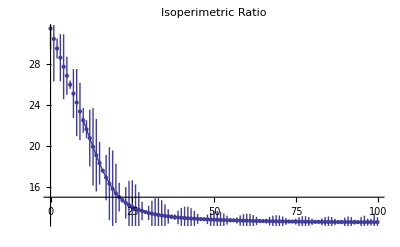
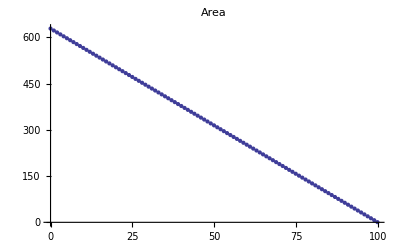
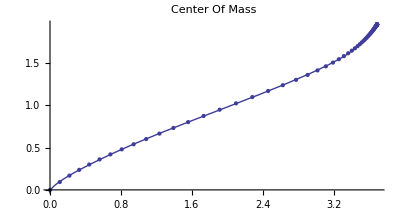
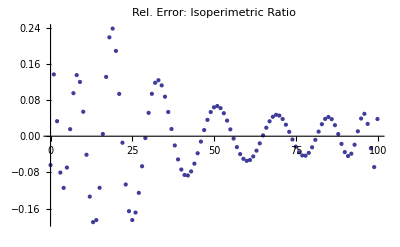
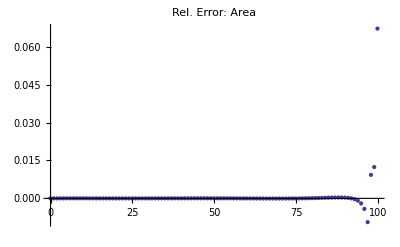
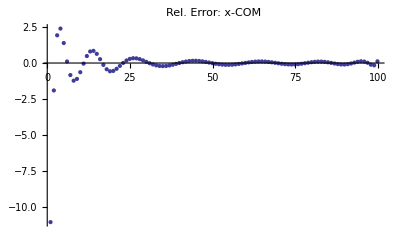
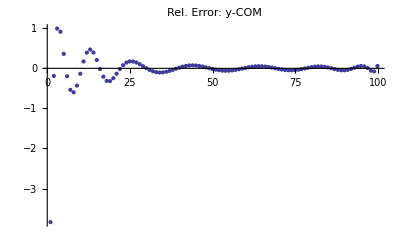
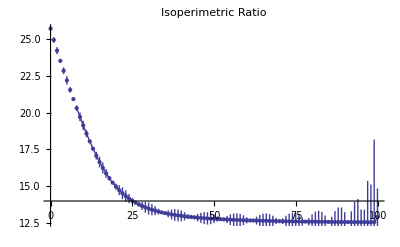
n     = | 1
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 2
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 3
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 4
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 5
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 6
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 7
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 8
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 9
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 10
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 11
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 12
FitPts= | 100
O(iso)  = | 16
O(A)  = | 6
O(COM) = | 14
IsoExp = | 2
AreaExp= | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{fitpts=100,isoorder=16,aorder=6,comorder=14},
TableForm[
Table[fullfits[num,fitpts,isoorder,aorder,comorder],{num,1,12}
]
]
]
```

### plots

#### evolution plots

```mathematica
Block[{evoplot, num1 = 2, num2 = 6, rescale = 3, axlabsize = 11, labsize=16,ticks, tickstyle,axlabel},
 
ticks = Ticks -> {Automatic, Automatic, {{0, 0}, {100/rescale, 100}}};
tickstyle=TicksStyle->Directive[5];axlabel=AxesLabel -> {Style[x,axlabsize], Style[y,axlabsize], Style[τ,axlabsize]};
 
 evoplot=
  GraphicsGrid[{
{evocenplot3d[num1,rescale, ticks, tickstyle,axlabel, AxesEdge -> {{-1, -1}, {1, -1}, {-1, -1}},ViewPoint->{1.3,-2.4,1.3}],evocenplot3d[num2,rescale, ticks, tickstyle,axlabel, AxesEdge -> {{-1, -1}, {1, -1}, {-1, -1}},ViewPoint->{1.3,-2.4,1.3}]},
{"(a)","(b)"}
},Alignment->Top];
 
 Export["plots/0EvolutionPlots.eps", evoplot];
 Export["/home/julian/latex/thesis/0EvolutionPlots.eps", evoplot];
 evoplot
 ]
```

-Graphics-

#### COM trajectories

```mathematica
Block[{nmax=12,d=8,rescale=7,axlabsize=18,traplots},
traplots=
Show[
Table[
ParametricPlot3D[Flatten[{ Subscript[com, num][t],t/rescale}],{t,0,100},PlotRange->{{-8,4},{-4,4},{0,110/rescale}},Boxed->True,PlotStyle->{Hue[num/nmax],Thickness[.0035]},ViewPoint->{0.2,-2,2.2},Ticks->{Automatic,Automatic,{{0,0},{100/rescale,100}}},AxesLabel->{Style[x,axlabsize],Style[y,axlabsize],Style[τ,axlabsize]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}],
{num,1,nmax}
],
Graphics3D[
Prepend[Table[Text[Style[num,16],Flatten[{ Subscript[com, num][100],104/rescale}]],{num,1,nmax}],Point[{0,0,0}]]
]
];
Export["plots/0TrajectoriesOfCOMs.eps",traplots];
Export["/home/julian/latex/thesis/0TrajectoriesOfCOM.eps",traplots];
traplots
]
```

-Graphics3D-

#### check : com data - com fitted

```mathematica
Block[{num=12,scale=15},
ParametricPlot3D[{Flatten[{fmulti[num,t][[4]],t/scale}],Flatten[{Subscript[com, num][t],t/scale}]},{t,0,99.9},PerformanceGoal->"Speed",PlotRange->{{-10,4},{-4,4},{0,100}/scale}]
]
```

### Saving LICs

```mathematica
Evaluate[Table[{Subscript[l, num][t],Subscript[iso, num][t],Subscript[com, num][t]},{num,1,12}]]>>data/LICs20080820;
```

### Loading LICs

```mathematica
Block[{list,t,n,num},
list=<<data/LICs20080820;
n=Length@list;
ClearAll[iso,com];
Evaluate[Table[{Subscript[l, num][t_],Subscript[iso, num][t_],Subscript[com, num][t_]},{num,1,n}]]=list;
Print[n];
TableForm@Table[{num,Subscript[l, num][t],Subscript[iso, num][t],Subscript[com, num][t]},{num,1,n}]/.t->0
]
```

1 | 140.562 | 31.4451 | 0.00605874
0.00146651
2 | 127.08 | 25.7025 | -0.00107393
-0.00036986
3 | 141.031 | 31.6556 | -0.000495937
0.00083056
4 | 145.083 | 33.5004 | 0.000222757
-0.00105948
5 | 153.671 | 37.5839 | 0.000146196
0.00192853
6 | 131.74 | 27.622 | 0.000734173
0.00359339
7 | 127.356 | 25.8142 | -0.00194511
-0.00211309
8 | 124.357 | 24.6128 | -0.00110462
-0.00141391
9 | 161.737 | 41.6329 | 0.000384128
-0.0000260568
10 | 149.421 | 35.5342 | -0.0073648
-0.00141647
11 | 199.42 | 63.2932 | -0.00622621
-0.0128942
12 | 203.557 | 65.9464 | 0.0015791
0.00466482

## renormalization group flow

### Loading LICs

```mathematica
Block[{list,t,n,num},
list=<<data/LICs20080820;
n=Length@list;
ClearAll[l,iso,com];
Evaluate[Table[{Subscript[l, num][t_],Subscript[iso, num][t_],Subscript[com, num][t_]},{num,1,n}]]=list;
Print[n];
TableForm@Table[{num,Subscript[l, num][t],Subscript[iso, num][t],Subscript[com, num][t]},{num,1,n}]/.t->0
]
```

12

1 | 140.562 | 31.4451 | 0.00605874
0.00146651
2 | 127.08 | 25.7025 | -0.00107393
-0.00036986
3 | 141.031 | 31.6556 | -0.000495937
0.00083056
4 | 145.083 | 33.5004 | 0.000222757
-0.00105948
5 | 153.671 | 37.5839 | 0.000146196
0.00192853
6 | 131.74 | 27.622 | 0.000734173
0.00359339
7 | 127.356 | 25.8142 | -0.00194511
-0.00211309
8 | 124.357 | 24.6128 | -0.00110462
-0.00141391
9 | 161.737 | 41.6329 | 0.000384128
-0.0000260568
10 | 149.421 | 35.5342 | -0.0073648
-0.00141647
11 | 199.42 | 63.2932 | -0.00622621
-0.0128942
12 | 203.557 | 65.9464 | 0.0015791
0.00466482

### functions

#### partition function

```mathematica
ClearAll[zl,za];

Subscript[zl, n_Integer][t_]:=Sum[Exp[-Subscript[iso, num][t](1+(c[t]/.Subscript[csol, n][[1]])/Subscript[l, num][t])],{num,1,n}];

Subscript[za, n_Integer][t_]:=Sum[Exp[-Subscript[iso, num][t](1+(c[t]/.Subscript[csol, n][[1]])/(200π-2π t))],{num,1,n}];
```

#### RGF ODE

Solving the implicit first order differential equation for the coefficient.

```mathematica
Clear[rgfodel,rgfodea];

rgfodel[n_,tmax_:99.999,c0_:-290,cdefault_:False]:=
Block[{elist,z,pde,ceq,bc,c,tab},

elist=Range[1,n];

z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,elist}];
pde=Evaluate[D[z[t], t]] ==0;

If[
NumberQ[cdefault],
bc=c[0]==cdefault;,
ceq=1/z[0]Sum[Subscript[l, num][0] Exp[-Subscript[iso, num][0](1+c[0]/Subscript[l, num][0])] ,{num,elist}]==Sum[Subscript[l, num][0],{num,elist}]/n;
bc=c[0]==(c[0]/.FindRoot[ceq,{c[0],c0}]);,
Print["Error at determing c[0]"];
];

tab=Timing[Subscript[csol, n]=NDSolve[{pde,bc},c,{t,0,tmax}][[1]]];

Print["E",n,": c",n,"(0) = ",NumberForm[bc[[2]],{4,1}],",  computational time = ",NumberForm[tab[[1]]/60,{3,1}],",  ",tab[[2]]
];

];

rgfodea[n_,tmax_:99.999,c0_:-600,cdefault_:False]:=
Block[{elist,z,pde,ceq,bc,c,tab},

elist=Range[1,n];

z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/(200 π-2 π t))],{num,elist}];
pde=Evaluate[D[z[t], t]] ==0;

If[
NumberQ[cdefault],
bc=c[0]==cdefault;,
ceq=1/z[0]Sum[Subscript[l, num][0] Exp[-Subscript[iso, num][0](1+c[0]/(200 π))] ,{num,elist}]==Sum[Subscript[l, num][0],{num,elist}]/n;
bc=c[0]==(c[0]/.FindRoot[ceq,{c[0],c0}]);,
Print["Error at determing c[0]"];
];

tab=Timing[Subscript[csol, n]=NDSolve[{pde,bc},c,{t,0,tmax}][[1]]];

Print["E",n,": c",n,"(0) = ",NumberForm[bc[[2]],{4,1}],",  computational time = ",NumberForm[tab[[1]]/60,{3,1}],",  ",tab[[2]]
];

];
```

#### mean COM

```mathematica
ClearAll[meancoml,varcoml,meancoma,varcoma];

meancoml[n_Integer,t_]:=
1/Subscript[zl, n][0] Sum[Subscript[com, num][t]Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,1,n}]/. Subscript[csol, n];

varcoml[n_Integer,t_]:=Sqrt@Abs@(1/Subscript[zl, n][0] Sum[Subscript[com, num][t]^2 Exp[-Subscript[iso, num][t](1+(c[t]/. Subscript[csol, n])/Subscript[l, num][t])],{num,1,n}]-meancoml[n,t]^2);

meancoma[n_Integer,t_]:=
1/Subscript[za, n][0] Sum[Subscript[com, num][t]Exp[-Subscript[iso, num][t](1+c[t]/(200π-2π t))],{num,1,n}]/. Subscript[csol, n];

varcoma[n_Integer,t_]:=Sqrt@Abs@(1/Subscript[za, n][0] Sum[Subscript[com, num][t]^2 Exp[-Subscript[iso, num][t](1+(c[t]/. Subscript[csol, n])/(200π-2π t))],{num,1,n}]-meancoma[n,t]^2);
```

#### plotting

```mathematica
ClearAll[cplots,zplots,varcomplots,weightplotsl,weightplotsa];

col=4;row=3;tfin=99.999;

cplots[power_Integer,columns_Integer:col,rows_Integer:row,tfinal_:tfin,opts___]:=
Framed@Labeled[
TableForm[
Table[
Block[{n=columns(ii-1)+jj},
Plot[c[t]^power/. Subscript[csol, n],{t,0,tfinal},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->Style[Subscript["E", n],plotlabsize],opts]
],{ii,1,rows},{jj,1,columns}
]
],{Style[Subscript[c, M]^power,labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

zplots[partfunc_,columns_Integer:col,rows_Integer:row,tfinal_:tfin]:=
Framed@TableForm[
Table[
Block[{n=columns(ii-1)+jj,normfac},
normfac=Subscript[partfunc, n][0];
Plot[(Subscript[partfunc, n][t]/normfac-1)100,{t,0,tfinal},PerformanceGoal->"Speed",PlotRange->Full,PlotLabel->Style[Subscript["E", n],plotlabsize]]
],{ii,1,rows},{jj,1,columns}
]
];

varcomplots[variance_,columns_Integer:col,rows_Integer:row,tfinal_:tfin]:=
Framed@Labeled[TableForm[
Table[
Module[{n=columns(ii-1)+jj },
Plot[Sqrt@Norm@variance[n,t]^2,{t,0,tfinal},PlotLabel->Style[Subscript["E", n],plotlabsize],PlotRange->Full,PerformanceGoal->"Speed"]
],{ii,1,rows},{jj,1,columns}
]
],{Style[Subscript[Δ, M,COM],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

weightplotsl[partfunc_,tfinal_:tfin,nmax_:12,opts___]:=
Labeled[TableForm[
Table[
Module[{normfac},
normfac=Subscript[partfunc, ii][0];
Plot[1/normfac Exp[-Subscript[iso, jj][t](1+(c[t]/.Subscript[csol, ii][[1]])/Subscript[l, jj][t])],{t,0,tfinal},PlotLabel->TableForm[{{Style[Subscript["E", ii],plotlabsize],",",Style[Subscript["S", jj],plotlabsize]} }],PerformanceGoal->"Speed",opts]
],{ii,1,nmax},{jj,1,ii}
]
],{Style[Subscript[P, M],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

weightplotsa[partfunc_,tfinal_:tfin,nmax_:12,opts___]:=
Labeled[TableForm[
Table[
Module[{normfac},
normfac=Subscript[partfunc, ii][0];
Plot[1/normfac Exp[-Subscript[iso, jj][t](1+(c[t]/.Subscript[csol, ii][[1]])/(200π-2π t))],{t,0,tfinal},PlotLabel->TableForm[{{Style[Subscript["E", ii],plotlabsize],",",Style[Subscript["S", jj],plotlabsize]} }] ,PerformanceGoal->"Speed",opts]
],{ii,1,nmax},{jj,1,ii}
]
],{Style[Subscript[P, M],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];
```

#### prefactor & exponent fit for c(t)

```mathematica
Clear[c2fitL,vtabL,ktabL,c2fitA,vtabA,ktabA];

c2fitL[n_Integer,t1_,t2_,pts_:50]:=
Block[{data,expr,pars,cf},
data=Table[{t1 +(t2-t1)i/pts,(c[t1 +(t2-t1)i/pts]/.Subscript[csolL, n][[1]])^2},{i,0,pts}];
expr=k Abs[(100-t)]^v;
pars={{k,400},{v,1}};
cf=FindFit[data,expr,pars,t];
{Sqrt[k],v/2}/.cf
];

vtabL[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fitL[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[2]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
];

ktabL[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fitL[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[1]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
];

c2fitA[n_Integer,t1_,t2_,pts_:50]:=
Block[{data,expr,pars,cf},
data=Table[{t1 +(t2-t1)i/pts,(c[t1 +(t2-t1)i/pts]/.Subscript[csolA, n][[1]])^2},{i,0,pts}];
expr=k Abs[(100-t)]^v;
pars={{k,400},{v,1}};
cf=FindFit[data,expr,pars,t];
{Sqrt[k],v/2}/.cf
];

vtabA[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fitA[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[2]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
];

ktabA[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fitA[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[1]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
];
```

### regular action, c_0 derived from geometric mean

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,-270],{n,1,12}]
```

E1: c1(0) = -270.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

E2: c2(0) = -267.6,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -267.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -270.6,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -279.8,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -279.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -278.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -275.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -283.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -282.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -309.8,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -326.7,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820
```

#### plots

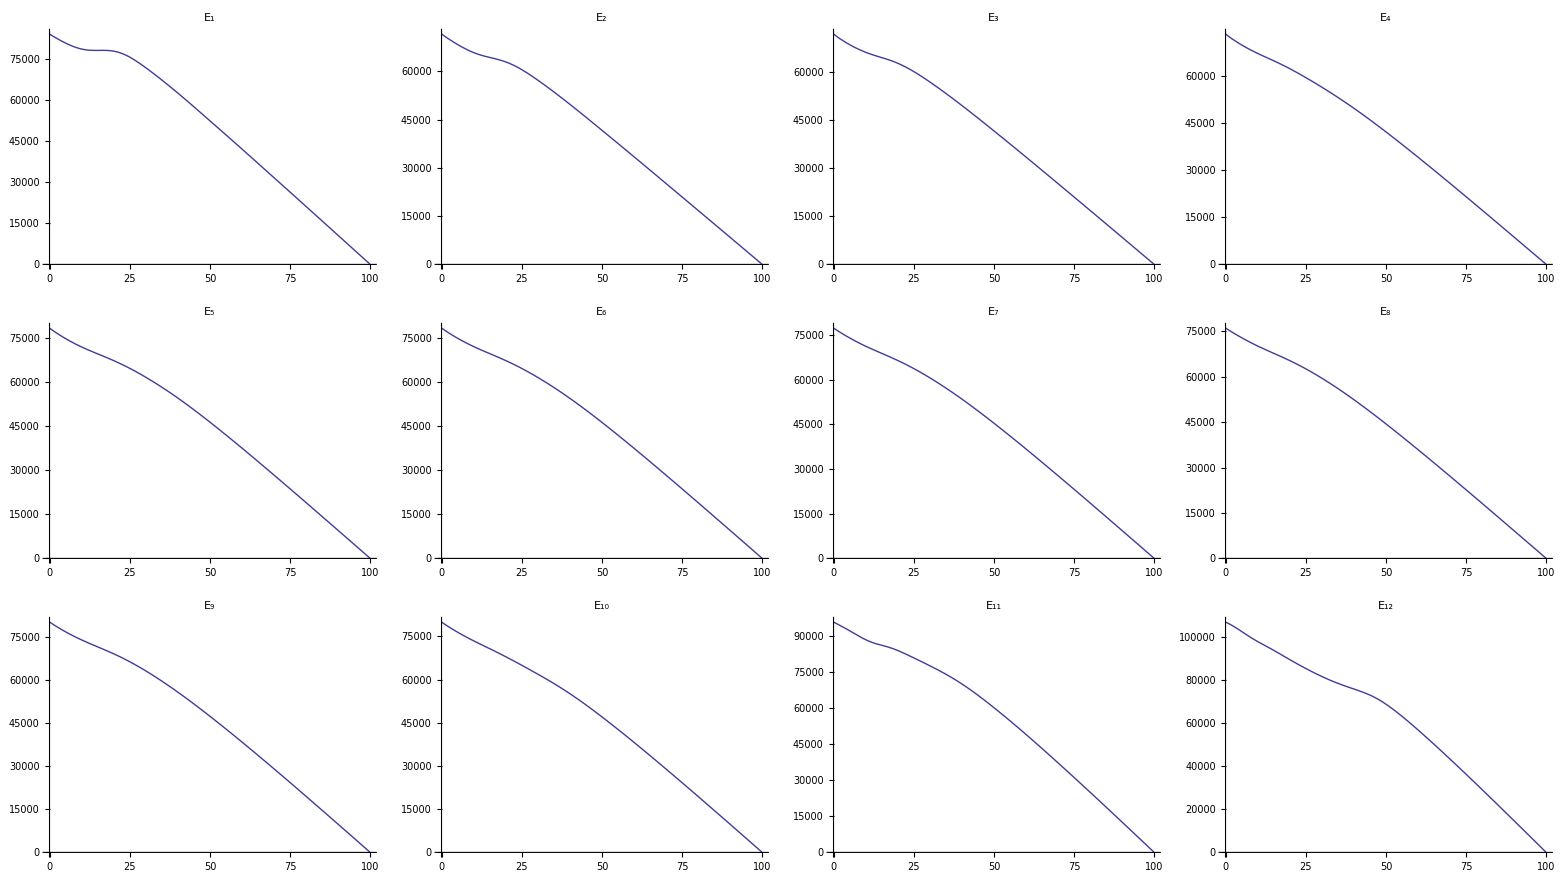
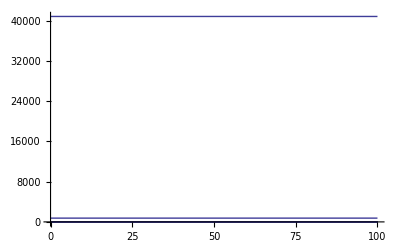
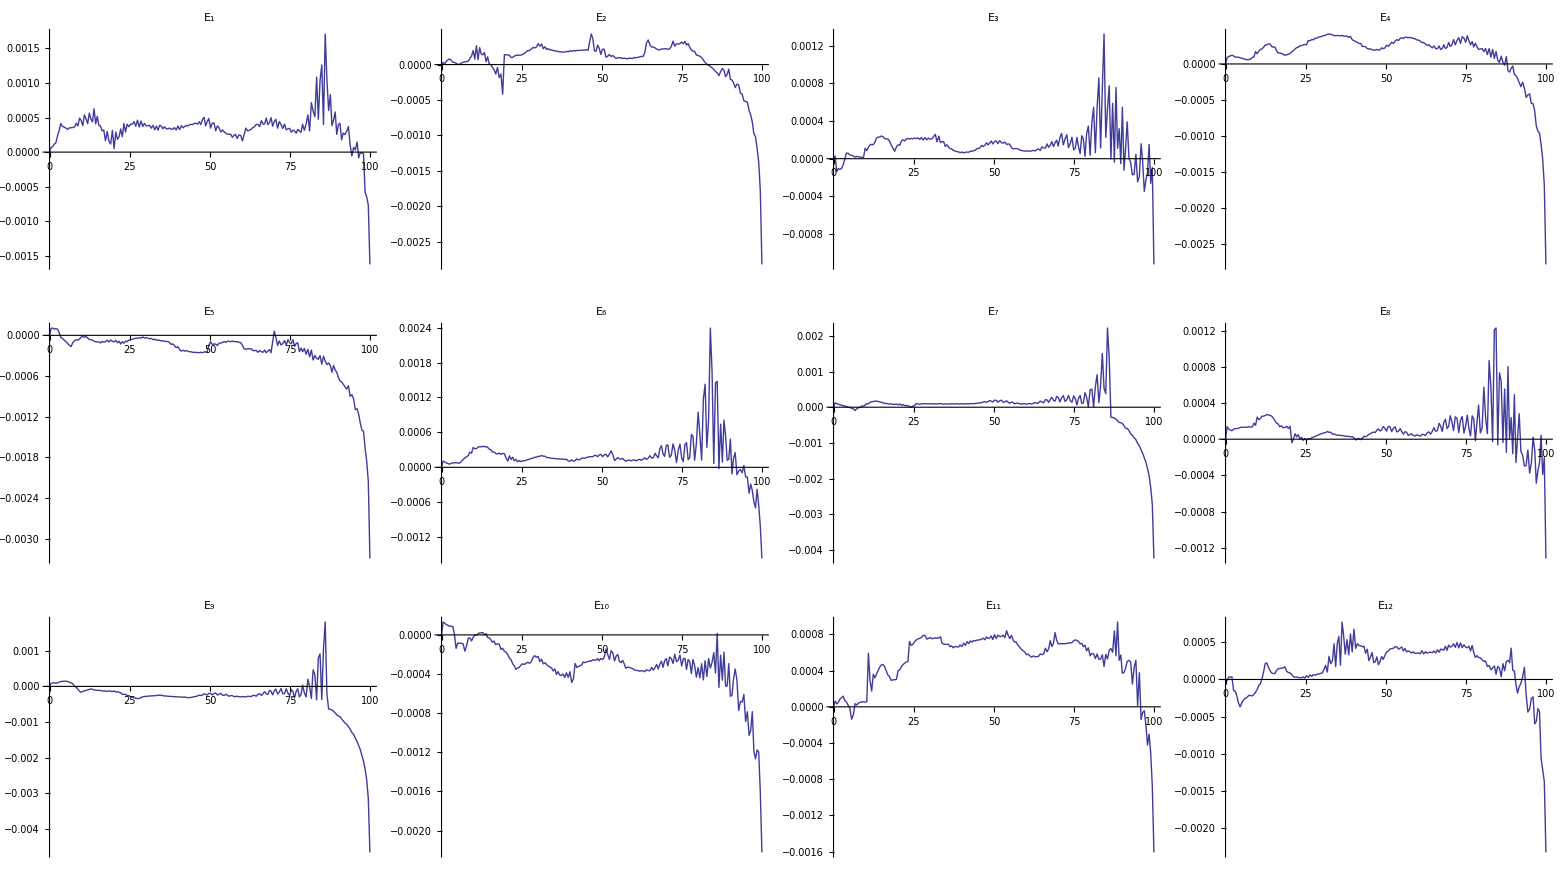
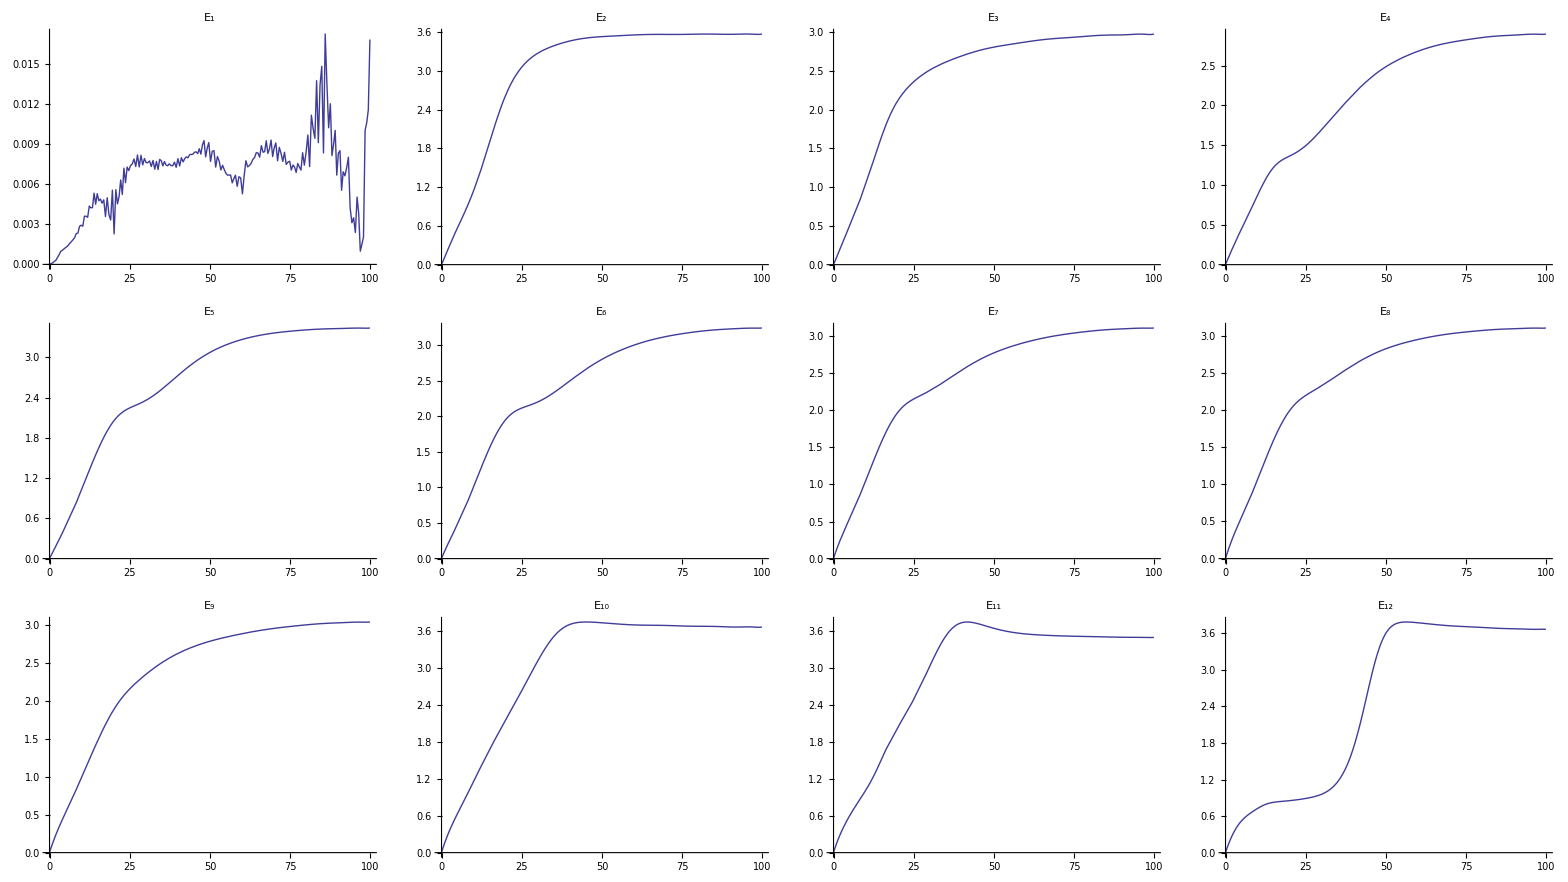
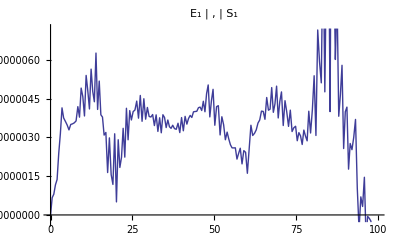
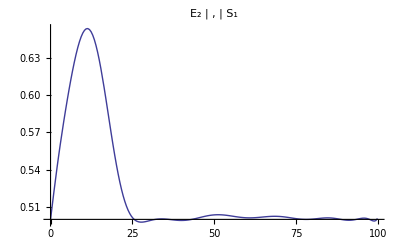
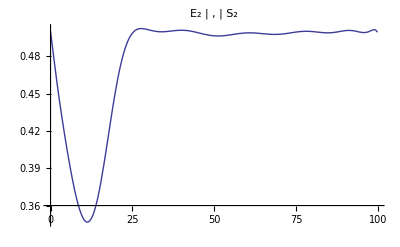
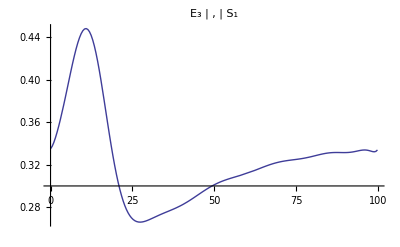
Coefficient
c_M^2 | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

Block[{list,n,c},
list=<<data/CIFsRA.N12.O16.20080820;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
];

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];
Export["plots/0CoefficientSquared.eps",cp];
Export["plots/0VarianceOfCOMReg.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Regular Action"}}]

]
```

### regular action, c_0=0

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,0],{n,1,12}]
```

E1: c1(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal0
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal0.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal0.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action, c_0=-500

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,-500],{n,1,12}]
```

E1: c1(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal-500
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal-500.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal-500.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action, c_0=-1000

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,-1000],{n,1,12}]
```

E1: c1(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal-1000
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal-1000.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal-1000.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action, c_0=-2000

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,-2000],{n,1,12}]
```

E1: c1(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -2000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal-2000
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal-2000.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal-2000.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action, c_0=500

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,500],{n,1,12}]
```

E1: c1(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = 500.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal500
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal-1000.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal-1000.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action, c_0=1000

#### solving RGF ODE

```mathematica
Do[rgfodel[n,99.99,0,1000],{n,1,12}]
```

E1: c1(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = 1000.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsRA.N12.O16.20080820.c0equal1000
```

#### plots

```mathematica
Block[{partitionfunction=zl,variance=varcoml,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[2,columns,rows,tmax];
zp=Block[{normfac},normfac=Subscript[partitionfunction, 1][0];Plot[Table[Subscript[partitionfunction, num][t]/normfac,{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed",PlotRange->Full]];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsl[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMReg.eps",vp];*)
Export["plots/0CoefficientSquared.c0equal1000.eps",cp];
Export["plots/0VarianceOfCOMReg.c0equal1000.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
}]

]
```

Coefficient
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=-200π (same as derived from geometric mean)

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,-200N@π],{n,1,12}]
```

E1: c1(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

E7: c7(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -628.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.9,noc,cp,zp,dzp,vp,wp},

Block[{list,n,c},
list=<<data/CIFsAATO.N12.O16.20080821;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
];

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];
Export["plots/0Coefficient.eps",cp];
Export["plots/0VarianceOfCOMAlt.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=0

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,0,0],{n,1,12}]
```

E1: c1(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = 0.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821.c0equals0
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.999,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];*)
Export["plots/0Coefficient.c0equals0.eps",cp];
Export["plots/0VarianceOfCOMAlt.c0equals0.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=-100π

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,0,-100N@Pi],{n,1,12}]
```

E1: c1(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -314.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821.c0equals-100Pi
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.99,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];*)
Export["plots/0Coefficient.c0equals-100Pi.eps",cp];
Export["plots/0VarianceOfCOMAlt.c0equals-100Pi.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=-150π

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,0,-150N@Pi],{n,1,12}]
```

E1: c1(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -471.2,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821.c0equals-150Pi
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.99,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];*)
Export["plots/0Coefficient.c0equals-150Pi.eps",cp];
Export["plots/0VarianceOfCOMAlt.c0equals-150Pi.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=-300π

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,0,-300N@π],{n,1,12}]
```

E1: c1(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -942.5,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821.c0equals-300Pi
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.99,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];*)
Export["plots/0Coefficient.c0equals-300Pi.eps",cp];
Export["plots/0VarianceOfCOMAlt.c0equals-300Pi.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action, c_0=-400π

#### solving RGF ODE

```mathematica
Do[rgfodea[n,99.99,0,-400N@π],{n,1,12}]
```

E1: c1(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E2: c2(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E3: c3(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E4: c4(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E5: c5(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E6: c6(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E7: c7(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E8: c8(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E9: c9(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E10: c10(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E11: c11(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

E12: c12(0) = -1257.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,99.99}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,12}]]>>data/CIFsAATO.N12.O16.20080821.c0equals-400Pi
```

#### plots

```mathematica
Block[{partitionfunction=za,variance=varcoma,columns=4,rows=3,tmax=99.99,noc,cp,zp,dzp,vp,wp},

noc=columns rows;
cp=cplots[1,columns,rows,tmax];
zp=Plot[Table[Subscript[partitionfunction, num][t],{num,1,noc}],{t,0,tfin},PerformanceGoal->"Speed"];
dzp=zplots[partitionfunction,columns,rows,tmax];
vp=varcomplots[variance,columns,rows,tmax];
wp=weightplotsa[partitionfunction,tmax,noc];

(*Export["/home/julian/latex/thesis/0Coefficient.eps",cp];
Export["/home/julian/latex/thesis/0VarianceOfCOMAlt.eps",vp];*)
Export["plots/0Coefficient.c0equals-400Pi.eps",cp];
Export["plots/0VarianceOfCOMAlt.c0equals-400Pi.eps",vp];

TableForm[{
"Coefficient",cp,
"Partition Functions",zp,
"Partition Functions: Derivations from constance",dzp,
"Variance Of Mean COM",vp,
"Statistical Weights",wp
},TableHeadings->{None,{"Alternative Action"}}]

]
```

Coefficient
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Functions
-Graphics-
Partition Functions: Derivations from constance
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance Of Mean COM
Δ_(M,COM) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Statistical Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### former version: plots, tables, code, mean field fits

! This notebook is an updated version for the embedded curves. The mean field coefficient fits are not yet implemented!

#### RGF ODE, alternative action: partition function plots

```mathematica
Do[coPDEactionA[i,-0],{i,1,n}]
```

E1: c1(0) = 0,    computational time = 0.008001,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E2: c2(0) = 0,    computational time = 0.012001,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E3: c3(0) = 0,    computational time = 0.012,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E4: c4(0) = 0,    computational time = 0.016001,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E5: c5(0) = 0,    computational time = 0.016001,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E6: c6(0) = 0,    computational time = 0.020001,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E7: c7(0) = 0,    computational time = 0.028002,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E8: c8(0) = 0,    computational time = 0.028002,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E9: c9(0) = 0,    computational time = 0.032002,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E10: c10(0) = 0,    computational time = 0.036003,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E11: c11(0) = 0,    computational time = 0.040002,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

E12: c12(0) = 0,    computational time = 0.072004,    {c→InterpolatingFunction[{{0.,99.9}},<>]}

```mathematica
TableForm[Table[Plot[ZactionA[3(i-1)+j,t]/ZactionA[3(i-1)+j,0]-1,{t,0,99.9},PerformanceGoal->"Speed",PlotRange->All,PlotLabel->3(i-1)+j],{i,1,4},{j,1,3}],TableHeadings->{None,{"Partition functions A"}}]
```

Partition functions A |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### export plots & tables

```mathematica
Export["tables/LCExponentInt91to100.eps",vtabL[n,90.9,99.9]];
Export["tables/LCExponentInt01to100.eps",vtabL[n,0.9,99.9]];
```

```mathematica
Export["tables/LCCoefficientInt91to100.eps",ktabL[n,90.9,99.9]];
Export["tables/LCCoefficientInt01to100.eps",ktabL[n,0.9,99.9]];
```

```mathematica
Export["tables/A-0CExponentInt91to100.eps",vtabA[n,90.9,99.9]];
Export["tables/A-0CExponentInt01to100.eps",vtabA[n,0.9,99.9]];
```

```mathematica
Export["tables/A-0CCoefficientInt91to100.eps",ktabA[n,90.9,99.9]];
Export["tables/A-0CCoefficientInt01to100.eps",ktabA[n,0.9,99.9]];
```

#### mean COM: plots of intersections, variance plots, table of variance

```mathematica
mcom3dL=meanCOMplot3dL[n,10]
```

-Graphics3D-

```mathematica
Export["plots/LPlot3DMeanCOM.eps",mcom3dL];
```

```mathematica
varplotsL=
TableForm[
Table[
ListPlot[Table[{99.9t/100,Norm@varCOMActionL[4(i-1)+j,99.9t/100]},{t,0,100,2}],
PlotRange->All,PerformanceGoal->"Speed",PlotLabel->Style[Subscript["E", 4(i-1)+j]]
],{i,1,3},{j,1,4}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["plots/LPlotsVariance.eps",varplotsL];
```

```mathematica
vartabL=Block[{nn=n,pts=99},
TableForm[
Table[Norm@varCOMActionL[i,99.9 j/pts],{j,0,pts},{i,2,nn}
],TableHeadings->{Table[99.9 j/pts,{j,0,pts}],Range[2,nn]}
]
]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 5.464×10^-8 | 2.28594×10^-7 | 2.33375×10^-7 | 2.3744×10^-7 | 3.20728×10^-7 | 3.34623×10^-7 | 3.73988×10^-7 | 3.50583×10^-7 | 3.33123×10^-7 | 2.76147×10^-7 | 2.36784×10^-7
1.00909 | 0.124142 | 0.105016 | 0.101908 | 0.0997237 | 0.11253 | 0.134497 | 0.141648 | 0.133469 | 0.168292 | 0.163693 | 0.157499
2.01818 | 0.239904 | 0.203628 | 0.192475 | 0.192413 | 0.207931 | 0.244186 | 0.256638 | 0.241779 | 0.299586 | 0.288363 | 0.274573
3.02727 | 0.352112 | 0.301155 | 0.279407 | 0.285466 | 0.300128 | 0.345497 | 0.361586 | 0.341186 | 0.417974 | 0.399595 | 0.373733
4.03636 | 0.462825 | 0.400346 | 0.365544 | 0.381691 | 0.393421 | 0.443723 | 0.462074 | 0.4367 | 0.529857 | 0.502906 | 0.457119
5.04545 | 0.573359 | 0.501115 | 0.45152 | 0.48165 | 0.489058 | 0.541161 | 0.560817 | 0.530303 | 0.638093 | 0.601909 | 0.528484
6.05455 | 0.68474 | 0.604714 | 0.538076 | 0.586042 | 0.588256 | 0.639729 | 0.659958 | 0.623529 | 0.744563 | 0.692668 | 0.582588
7.06364 | 0.797954 | 0.711334 | 0.625121 | 0.69477 | 0.691247 | 0.740432 | 0.760725 | 0.717204 | 0.851125 | 0.777972 | 0.626847
8.07273 | 0.914126 | 0.821063 | 0.712189 | 0.807413 | 0.797845 | 0.843734 | 0.863751 | 0.8118 | 0.955693 | 0.856556 | 0.662754
9.08182 | 1.03461 | 0.934014 | 0.798507 | 0.923302 | 0.907533 | 0.949613 | 0.969147 | 0.907489 | 1.06071 | 0.933826 | 0.695422
10.0909 | 1.16093 | 1.05034 | 0.883005 | 1.04156 | 1.01951 | 1.05761 | 1.07656 | 1.00419 | 1.16602 | 1.0136 | 0.726362
11.1 | 1.29465 | 1.17007 | 0.964316 | 1.16111 | 1.13271 | 1.16681 | 1.18514 | 1.10157 | 1.27123 | 1.09984 | 0.755445
12.1091 | 1.43693 | 1.29288 | 1.04082 | 1.28074 | 1.24586 | 1.27627 | 1.29404 | 1.19934 | 1.37601 | 1.19574 | 0.781276
13.1182 | 1.58818 | 1.41779 | 1.11078 | 1.39911 | 1.35752 | 1.38448 | 1.40179 | 1.29685 | 1.47999 | 1.30625 | 0.804288
14.1273 | 1.74746 | 1.54285 | 1.17263 | 1.51477 | 1.46611 | 1.48996 | 1.50701 | 1.39347 | 1.58293 | 1.42029 | 0.81839
15.1364 | 1.9122 | 1.66522 | 1.22527 | 1.62616 | 1.56995 | 1.59112 | 1.60816 | 1.48836 | 1.68466 | 1.53879 | 0.828033
16.1455 | 2.07812 | 1.78139 | 1.26837 | 1.73161 | 1.66729 | 1.68631 | 1.7037 | 1.58052 | 1.78504 | 1.65513 | 0.834764
17.1545 | 2.23981 | 1.88789 | 1.30256 | 1.82936 | 1.75642 | 1.77395 | 1.79217 | 1.66883 | 1.88397 | 1.76419 | 0.840137
18.1636 | 2.3919 | 1.98222 | 1.32944 | 1.9178 | 1.83591 | 1.85275 | 1.87238 | 1.75223 | 1.98146 | 1.86454 | 0.845223
19.1727 | 2.53036 | 2.0635 | 1.35137 | 1.99567 | 1.90478 | 1.92187 | 1.94358 | 1.82986 | 2.07768 | 1.95802 | 0.850552
20.1818 | 2.65323 | 2.13253 | 1.37101 | 2.06227 | 1.96266 | 1.98106 | 2.00554 | 1.90123 | 2.17292 | 2.04763 | 0.856309
21.1909 | 2.76052 | 2.19126 | 1.39081 | 2.11764 | 2.00988 | 2.03068 | 2.05858 | 1.96622 | 2.2676 | 2.13608 | 0.862519
22.2 | 2.85358 | 2.24198 | 1.41267 | 2.16251 | 2.0474 | 2.07167 | 2.10362 | 2.02513 | 2.36216 | 2.22531 | 0.86918
23.2091 | 2.93429 | 2.28679 | 1.43777 | 2.19836 | 2.07676 | 2.10543 | 2.14179 | 2.0785 | 2.457 | 2.31672 | 0.87632
24.2182 | 3.00455 | 2.3273 | 1.4667 | 2.22731 | 2.09989 | 2.13375 | 2.17478 | 2.12727 | 2.55266 | 2.41151 | 0.884081
25.2273 | 3.06604 | 2.36462 | 1.49949 | 2.25129 | 2.11868 | 2.15819 | 2.20394 | 2.1721 | 2.64898 | 2.50997 | 0.892618
26.2364 | 3.12011 | 2.39939 | 1.53592 | 2.27265 | 2.13517 | 2.1805 | 2.23083 | 2.21392 | 2.746 | 2.61246 | 0.9023
27.2455 | 3.1678 | 2.43194 | 1.57551 | 2.29336 | 2.15103 | 2.20206 | 2.2567 | 2.25344 | 2.84348 | 2.71891 | 0.913633
28.2545 | 3.20998 | 2.46242 | 1.6177 | 2.31499 | 2.16757 | 2.22391 | 2.28246 | 2.29117 | 2.94084 | 2.82868 | 0.927298
29.2636 | 3.24734 | 2.49087 | 1.66188 | 2.33864 | 2.18572 | 2.24671 | 2.30871 | 2.32744 | 3.03721 | 2.94061 | 0.944169
30.2727 | 3.28048 | 2.51732 | 1.70747 | 2.36496 | 2.20602 | 2.27082 | 2.33575 | 2.3624 | 3.13146 | 3.05298 | 0.965328
31.2818 | 3.30992 | 2.54182 | 1.75395 | 2.39422 | 2.22872 | 2.29632 | 2.36362 | 2.3961 | 3.22223 | 3.16361 | 0.992075
32.2909 | 3.33611 | 2.56445 | 1.80087 | 2.42638 | 2.25382 | 2.3231 | 2.39224 | 2.42842 | 3.308 | 3.26989 | 1.02594
33.3 | 3.35946 | 2.58536 | 1.84785 | 2.46122 | 2.28116 | 2.35095 | 2.4214 | 2.45954 | 3.3875 | 3.36934 | 1.06882
34.3091 | 3.38031 | 2.6047 | 1.89461 | 2.49834 | 2.31047 | 2.3796 | 2.45087 | 2.48926 | 3.4594 | 3.4594 | 1.1222
35.3182 | 3.39897 | 2.62268 | 1.94091 | 2.5373 | 2.34142 | 2.40874 | 2.48037 | 2.51754 | 3.52796 | 3.54376 | 1.18974
36.3273 | 3.41568 | 2.63949 | 1.98657 | 2.57762 | 2.37365 | 2.4381 | 2.50967 | 2.54438 | 3.58087 | 3.60796 | 1.27161
37.3364 | 3.43068 | 2.65534 | 2.03145 | 2.61881 | 2.40683 | 2.46742 | 2.53857 | 2.56979 | 3.62498 | 3.65908 | 1.37163
38.3455 | 3.44416 | 2.6704 | 2.07542 | 2.66042 | 2.4406 | 2.49646 | 2.56687 | 2.5938 | 3.66045 | 3.69714 | 1.49217
39.3545 | 3.4563 | 2.68482 | 2.11838 | 2.70202 | 2.47466 | 2.52504 | 2.59445 | 2.61647 | 3.68783 | 3.72285 | 1.6352
40.3636 | 3.46723 | 2.6987 | 2.16019 | 2.74324 | 2.50873 | 2.55301 | 2.62119 | 2.63786 | 3.70799 | 3.73761 | 1.80183
41.3727 | 3.4771 | 2.71212 | 2.20077 | 2.78373 | 2.54254 | 2.58024 | 2.64701 | 2.65804 | 3.72203 | 3.74316 | 1.99159
42.3818 | 3.48602 | 2.72511 | 2.23998 | 2.82322 | 2.57588 | 2.60664 | 2.67185 | 2.67709 | 3.7311 | 3.7414 | 2.20176
43.3909 | 3.49408 | 2.73767 | 2.27775 | 2.86147 | 2.60857 | 2.63212 | 2.69567 | 2.69509 | 3.7363 | 3.73416 | 2.42676
44.4 | 3.50138 | 2.74977 | 2.31396 | 2.8983 | 2.64045 | 2.65665 | 2.71844 | 2.71211 | 3.7386 | 3.72309 | 2.65802
45.4091 | 3.50798 | 2.76139 | 2.34854 | 2.93358 | 2.67141 | 2.68019 | 2.74015 | 2.72821 | 3.73881 | 3.70957 | 2.88471
46.4182 | 3.51396 | 2.77248 | 2.38143 | 2.96721 | 2.70135 | 2.70271 | 2.76079 | 2.74347 | 3.73759 | 3.6947 | 3.09542
47.4273 | 3.51937 | 2.78301 | 2.41262 | 2.99913 | 2.73021 | 2.72421 | 2.78038 | 2.75793 | 3.73539 | 3.67931 | 3.28037
48.4364 | 3.52428 | 2.79295 | 2.44208 | 3.02933 | 2.75794 | 2.7447 | 2.79892 | 2.77164 | 3.73256 | 3.66401 | 3.43338
49.4455 | 3.52874 | 2.8023 | 2.46985 | 3.0578 | 2.78454 | 2.76416 | 2.81642 | 2.78465 | 3.72933 | 3.64922 | 3.55273
50.4545 | 3.53279 | 2.81106 | 2.49598 | 3.08458 | 2.80999 | 2.7827 | 2.83297 | 2.79705 | 3.72585 | 3.63521 | 3.64058
51.4636 | 3.53648 | 2.81926 | 2.52052 | 3.10971 | 2.8343 | 2.80031 | 2.84858 | 2.80885 | 3.7222 | 3.62213 | 3.70167
52.4727 | 3.53983 | 2.82694 | 2.54359 | 3.13324 | 2.8575 | 2.81705 | 2.86331 | 2.82011 | 3.71846 | 3.61006 | 3.74173
53.4818 | 3.54288 | 2.83415 | 2.56527 | 3.15525 | 2.87962 | 2.83295 | 2.87721 | 2.83087 | 3.71468 | 3.59903 | 3.76625
54.4909 | 3.54565 | 2.84097 | 2.58566 | 3.17589 | 2.90076 | 2.84814 | 2.89039 | 2.84121 | 3.71094 | 3.58901 | 3.77987
55.5 | 3.54816 | 2.84746 | 2.60489 | 3.19506 | 2.9208 | 2.86254 | 2.90279 | 2.85111 | 3.70726 | 3.57994 | 3.78616
56.5091 | 3.55044 | 2.85369 | 2.62303 | 3.21295 | 2.93989 | 2.87626 | 2.91455 | 2.86064 | 3.70374 | 3.57177 | 3.78769
57.5182 | 3.55249 | 2.8597 | 2.64019 | 3.22963 | 2.95803 | 2.88936 | 2.92572 | 2.86984 | 3.70044 | 3.56443 | 3.78623
58.5273 | 3.55435 | 2.86556 | 2.65644 | 3.24517 | 2.97528 | 2.90188 | 2.93635 | 2.87873 | 3.69743 | 3.55786 | 3.78293
59.5364 | 3.55602 | 2.87129 | 2.67184 | 3.25965 | 2.99167 | 2.91385 | 2.94648 | 2.88735 | 3.69477 | 3.55199 | 3.77853
60.5455 | 3.55753 | 2.87692 | 2.68644 | 3.27315 | 3.00725 | 2.92531 | 2.95615 | 2.89569 | 3.6925 | 3.54677 | 3.77348
61.5545 | 3.55888 | 2.88243 | 2.70029 | 3.28574 | 3.02204 | 2.93629 | 2.96539 | 2.90379 | 3.69063 | 3.54214 | 3.76806
62.5636 | 3.5601 | 2.88783 | 2.7134 | 3.29748 | 3.03608 | 2.9468 | 2.97422 | 2.91163 | 3.68916 | 3.53804 | 3.76245
63.5727 | 3.56118 | 2.89308 | 2.7258 | 3.30842 | 3.0494 | 2.95686 | 2.98265 | 2.91922 | 3.68805 | 3.53443 | 3.75679
64.5818 | 3.56215 | 2.89815 | 2.73749 | 3.31863 | 3.06205 | 2.96648 | 2.9907 | 2.92656 | 3.68722 | 3.53125 | 3.75118
65.5909 | 3.56301 | 2.90301 | 2.74849 | 3.32815 | 3.07404 | 2.97567 | 2.99835 | 2.93364 | 3.6866 | 3.52845 | 3.74571
66.6 | 3.56377 | 2.90762 | 2.75882 | 3.33702 | 3.08542 | 2.98444 | 3.00563 | 2.94045 | 3.68608 | 3.52599 | 3.74049
67.6091 | 3.56445 | 2.91197 | 2.7685 | 3.34526 | 3.0962 | 2.99279 | 3.01251 | 2.94699 | 3.68557 | 3.52383 | 3.73559
68.6182 | 3.56505 | 2.91604 | 2.77756 | 3.35293 | 3.1064 | 3.0007 | 3.01898 | 2.95322 | 3.68494 | 3.52189 | 3.73107
69.6273 | 3.56558 | 2.91982 | 2.78604 | 3.36004 | 3.11607 | 3.00824 | 3.0251 | 2.9592 | 3.68416 | 3.52018 | 3.727
70.6364 | 3.56605 | 2.92335 | 2.79399 | 3.36663 | 3.12524 | 3.01541 | 3.03087 | 2.96491 | 3.68317 | 3.51864 | 3.72339
71.6455 | 3.56647 | 2.92664 | 2.80145 | 3.37273 | 3.13392 | 3.02221 | 3.0363 | 2.97036 | 3.68193 | 3.51722 | 3.7202
72.6545 | 3.56683 | 2.92973 | 2.80848 | 3.37836 | 3.14213 | 3.02867 | 3.04141 | 2.97557 | 3.68048 | 3.51587 | 3.71736
73.6636 | 3.56714 | 2.93268 | 2.81513 | 3.38356 | 3.1499 | 3.0348 | 3.04623 | 2.98055 | 3.67885 | 3.51457 | 3.7148
74.6727 | 3.56741 | 2.93552 | 2.82144 | 3.38837 | 3.15725 | 3.04065 | 3.0508 | 2.98532 | 3.67712 | 3.51328 | 3.7124
75.6818 | 3.56764 | 2.9383 | 2.82747 | 3.39282 | 3.16419 | 3.04623 | 3.05515 | 2.98992 | 3.6754 | 3.51199 | 3.71004
76.6909 | 3.56783 | 2.94105 | 2.83323 | 3.39696 | 3.17075 | 3.05155 | 3.05931 | 2.99435 | 3.67378 | 3.51067 | 3.70763
77.7 | 3.568 | 2.94379 | 2.83875 | 3.40082 | 3.17695 | 3.05663 | 3.06329 | 2.99862 | 3.67235 | 3.50933 | 3.70508
78.7091 | 3.56813 | 2.94651 | 2.844 | 3.40443 | 3.1828 | 3.06149 | 3.06713 | 3.00274 | 3.67118 | 3.50798 | 3.70235
79.7182 | 3.56824 | 2.9492 | 2.84899 | 3.40781 | 3.18831 | 3.06613 | 3.0708 | 3.00672 | 3.67029 | 3.50664 | 3.69943
80.7273 | 3.56834 | 2.95181 | 2.85369 | 3.41099 | 3.19349 | 3.07053 | 3.07433 | 3.01053 | 3.66966 | 3.50533 | 3.69636
81.7364 | 3.56841 | 2.9543 | 2.85806 | 3.41395 | 3.19835 | 3.0747 | 3.07765 | 3.01415 | 3.66922 | 3.50405 | 3.69321
82.7455 | 3.56847 | 2.95661 | 2.86209 | 3.41674 | 3.20289 | 3.07861 | 3.0808 | 3.01758 | 3.66887 | 3.50286 | 3.69012
83.7545 | 3.56853 | 2.95868 | 2.86576 | 3.41926 | 3.20713 | 3.08225 | 3.0837 | 3.02077 | 3.66847 | 3.50173 | 3.68719
84.7636 | 3.56855 | 2.96052 | 2.86909 | 3.4216 | 3.21104 | 3.08561 | 3.08634 | 3.02371 | 3.66788 | 3.50072 | 3.68457
85.7727 | 3.56859 | 2.96207 | 2.8721 | 3.42363 | 3.21464 | 3.08868 | 3.0887 | 3.02638 | 3.66698 | 3.49978 | 3.68234
86.7818 | 3.56859 | 2.96339 | 2.87484 | 3.42544 | 3.21796 | 3.09148 | 3.09079 | 3.0288 | 3.66572 | 3.4989 | 3.68052
87.7909 | 3.56861 | 2.96455 | 2.87739 | 3.42701 | 3.22101 | 3.09401 | 3.09263 | 3.03096 | 3.66413 | 3.49808 | 3.67906
88.8 | 3.56863 | 2.96561 | 2.87981 | 3.42836 | 3.2238 | 3.09631 | 3.09426 | 3.03291 | 3.66232 | 3.49726 | 3.67784
89.8091 | 3.56863 | 2.96668 | 2.88216 | 3.42953 | 3.22634 | 3.09841 | 3.09574 | 3.0347 | 3.66054 | 3.4964 | 3.67667
90.8182 | 3.56863 | 2.96783 | 2.88444 | 3.4306 | 3.22866 | 3.10036 | 3.09714 | 3.03638 | 3.65906 | 3.49554 | 3.67538
91.8273 | 3.56863 | 2.96904 | 2.88659 | 3.43162 | 3.23074 | 3.10218 | 3.0985 | 3.03799 | 3.65818 | 3.49466 | 3.67382
92.8364 | 3.56864 | 2.97028 | 2.88846 | 3.43266 | 3.23259 | 3.10388 | 3.09989 | 3.03957 | 3.65813 | 3.49393 | 3.67203
93.8455 | 3.56864 | 2.97138 | 2.88987 | 3.43374 | 3.23419 | 3.10543 | 3.10128 | 3.04108 | 3.65884 | 3.49334 | 3.67013
94.8545 | 3.56862 | 2.97209 | 2.89061 | 3.43477 | 3.23549 | 3.10675 | 3.10255 | 3.04243 | 3.65995 | 3.49303 | 3.66851
95.8636 | 3.56859 | 2.97226 | 2.89073 | 3.4356 | 3.23646 | 3.10775 | 3.10352 | 3.04347 | 3.66071 | 3.49301 | 3.66764
96.8727 | 3.56856 | 2.97206 | 2.8908 | 3.43598 | 3.23718 | 3.10834 | 3.10392 | 3.04399 | 3.66004 | 3.49306 | 3.66772
97.8818 | 3.56894 | 2.97281 | 2.89282 | 3.43573 | 3.23803 | 3.10869 | 3.10366 | 3.04392 | 3.65696 | 3.49239 | 3.66792
98.8909 | 3.56854 | 2.97641 | 2.90019 | 3.43422 | 3.23944 | 3.1089 | 3.1024 | 3.04293 | 3.65106 | 3.48869 | 3.66442
99.9 | 3.55595 | 2.97851 | 2.90965 | 3.4267 | 3.23806 | 3.10601 | 3.09722 | 3.0386 | 3.64297 | 3.47631 | 3.64742

```mathematica
Export["tables/LVariance.eps",vartabL];
```

```mathematica
mcom3dA=meanCOMplot3dA[n,10]
```

-Graphics3D-

```mathematica
Export["plots/A-0Plot3DMeanCOM.eps",mcom3dA];
```

```mathematica
varplotsA=
TableForm[
Table[
ListPlot[Table[{99.9t/100,Norm@varCOMActionA[4(i-1)+j,99.9t/100]},{t,0,100,2}],
PlotRange->All,PerformanceGoal->"Speed",PlotLabel->Style[Subscript["E", 4(i-1)+j]]
],{i,1,3},{j,1,4}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["plots/A-0PlotsVariance.eps",varplotsA];
```

```mathematica
vartabA=Block[{nn=n,pts=99},
TableForm[
Table[Norm@varCOMActionA[i,99.9 j/pts],{j,0,pts},{i,2,nn}
],TableHeadings->{Table[99.9 j/pts,{j,0,pts}],Range[2,nn]}
]
]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 6.16943×10^-9 | 2.24024×10^-8 | 2.28994×10^-8 | 2.29037×10^-8 | 2.13781×10^-7 | 2.8487×10^-7 | 3.94607×10^-7 | 3.94607×10^-7 | 3.94605×10^-7 | 3.94605×10^-7 | 3.94605×10^-7
1.00909 | 0.0140967 | 0.0172943 | 0.0176003 | 0.0176012 | 0.101768 | 0.104664 | 0.0592379 | 0.0592379 | 0.0592394 | 0.0592394 | 0.0592394
2.01818 | 0.0284937 | 0.0401442 | 0.0406562 | 0.0406584 | 0.192352 | 0.170273 | 0.0854203 | 0.0854203 | 0.0854217 | 0.0854217 | 0.0854217
3.02727 | 0.0440296 | 0.0722124 | 0.0728154 | 0.0728191 | 0.273184 | 0.209621 | 0.101009 | 0.101009 | 0.10101 | 0.10101 | 0.10101
4.03636 | 0.060686 | 0.115579 | 0.116179 | 0.116185 | 0.343969 | 0.232342 | 0.114836 | 0.114836 | 0.114837 | 0.114837 | 0.114837
5.04545 | 0.0786726 | 0.170501 | 0.17104 | 0.171047 | 0.40536 | 0.246077 | 0.130662 | 0.130662 | 0.130663 | 0.130663 | 0.130663
6.05455 | 0.0988811 | 0.235695 | 0.236147 | 0.236156 | 0.459178 | 0.25665 | 0.149433 | 0.149434 | 0.149434 | 0.149434 | 0.149434
7.06364 | 0.123048 | 0.308742 | 0.309104 | 0.309116 | 0.508223 | 0.268501 | 0.17066 | 0.170661 | 0.170661 | 0.170661 | 0.170661
8.07273 | 0.153845 | 0.386925 | 0.387207 | 0.387222 | 0.555861 | 0.284935 | 0.193548 | 0.193549 | 0.193549 | 0.193549 | 0.193549
9.08182 | 0.195069 | 0.468134 | 0.46835 | 0.46837 | 0.605384 | 0.308374 | 0.21778 | 0.217782 | 0.217782 | 0.217782 | 0.217782
10.0909 | 0.251919 | 0.551673 | 0.55184 | 0.551866 | 0.659757 | 0.340748 | 0.243941 | 0.243944 | 0.243944 | 0.243944 | 0.243944
11.1 | 0.331303 | 0.639103 | 0.639232 | 0.639266 | 0.722251 | 0.383861 | 0.273412 | 0.273417 | 0.273417 | 0.273417 | 0.273417
12.1091 | 0.441881 | 0.735262 | 0.735362 | 0.735407 | 0.797943 | 0.442281 | 0.310371 | 0.310378 | 0.310379 | 0.310379 | 0.310379
13.1182 | 0.593342 | 0.849165 | 0.849242 | 0.8493 | 0.89533 | 0.522704 | 0.359619 | 0.359631 | 0.359631 | 0.359631 | 0.359631
14.1273 | 0.794221 | 0.993422 | 0.993479 | 0.993552 | 1.02636 | 0.638144 | 0.430423 | 0.43044 | 0.43044 | 0.43044 | 0.43044
15.1364 | 1.04782 | 1.18017 | 1.18021 | 1.18029 | 1.20266 | 0.805074 | 0.535476 | 0.535499 | 0.5355 | 0.5355 | 0.5355
16.1455 | 1.34708 | 1.41344 | 1.41347 | 1.41356 | 1.42787 | 1.03534 | 0.688096 | 0.688124 | 0.688125 | 0.688125 | 0.688125
17.1545 | 1.67177 | 1.68252 | 1.68254 | 1.68263 | 1.69087 | 1.32485 | 0.895713 | 0.895745 | 0.895746 | 0.895749 | 0.895749
18.1636 | 1.99195 | 1.96275 | 1.96276 | 1.96284 | 1.96663 | 1.6487 | 1.15351 | 1.15354 | 1.15354 | 1.15355 | 1.15355
19.1727 | 2.27832 | 2.2251 | 2.2251 | 2.2252 | 2.22584 | 1.96915 | 1.44295 | 1.44298 | 1.44298 | 1.44301 | 1.44301
20.1818 | 2.51287 | 2.44823 | 2.44822 | 2.4484 | 2.44696 | 2.25223 | 1.73718 | 1.73721 | 1.73721 | 1.73725 | 1.73725
21.1909 | 2.69274 | 2.62457 | 2.62456 | 2.62501 | 2.62231 | 2.4804 | 2.01057 | 2.01058 | 2.01058 | 2.01055 | 2.01055
22.2 | 2.82619 | 2.7583 | 2.75829 | 2.75939 | 2.75597 | 2.65367 | 2.24671 | 2.24672 | 2.24672 | 2.24637 | 2.24637
23.2091 | 2.92574 | 2.85921 | 2.85919 | 2.86164 | 2.85781 | 2.78241 | 2.43935 | 2.43935 | 2.43935 | 2.43819 | 2.43819
24.2182 | 3.00291 | 2.93733 | 2.93731 | 2.94231 | 2.9382 | 2.87961 | 2.59136 | 2.59134 | 2.59134 | 2.58869 | 2.58869
25.2273 | 3.06599 | 3.00033 | 3.0003 | 3.00973 | 3.00535 | 2.95637 | 2.70958 | 2.70954 | 2.70954 | 2.70466 | 2.70466
26.2364 | 3.11997 | 3.05303 | 3.05301 | 3.0695 | 3.06482 | 3.02066 | 2.80193 | 2.80187 | 2.80187 | 2.79417 | 2.79417
27.2455 | 3.16744 | 3.09812 | 3.09809 | 3.125 | 3.11997 | 3.07761 | 2.87573 | 2.87565 | 2.87565 | 2.86483 | 2.86483
28.2545 | 3.20961 | 3.13697 | 3.13693 | 3.17796 | 3.17252 | 3.13021 | 2.93708 | 2.93697 | 2.93697 | 2.923 | 2.923
29.2636 | 3.24711 | 3.1704 | 3.17035 | 3.22889 | 3.223 | 3.17985 | 2.99055 | 2.99041 | 2.99041 | 2.97345 | 2.97345
30.2727 | 3.28039 | 3.19905 | 3.19898 | 3.27739 | 3.27105 | 3.22678 | 3.03922 | 3.03902 | 3.03903 | 3.01932 | 3.01932
31.2818 | 3.3099 | 3.22349 | 3.2234 | 3.3225 | 3.31572 | 3.27043 | 3.08469 | 3.08445 | 3.08445 | 3.06224 | 3.06224
32.2909 | 3.33611 | 3.24429 | 3.24418 | 3.3631 | 3.35593 | 3.30995 | 3.12748 | 3.12717 | 3.12717 | 3.10264 | 3.10264
33.3 | 3.35945 | 3.26196 | 3.26182 | 3.39834 | 3.39087 | 3.3446 | 3.16735 | 3.16696 | 3.16698 | 3.14021 | 3.14021
34.3091 | 3.3803 | 3.27689 | 3.27671 | 3.42784 | 3.42017 | 3.37396 | 3.20379 | 3.2033 | 3.20333 | 3.17434 | 3.17434
35.3182 | 3.39896 | 3.28937 | 3.28914 | 3.45171 | 3.44395 | 3.39806 | 3.23627 | 3.23568 | 3.23574 | 3.20447 | 3.20447
36.3273 | 3.41568 | 3.29963 | 3.29933 | 3.47041 | 3.46264 | 3.41719 | 3.26444 | 3.26374 | 3.26384 | 3.23021 | 3.23021
37.3364 | 3.43068 | 3.30782 | 3.30745 | 3.48453 | 3.47684 | 3.43182 | 3.28817 | 3.28734 | 3.28752 | 3.25144 | 3.25144
38.3455 | 3.44414 | 3.31409 | 3.31362 | 3.49469 | 3.48715 | 3.44247 | 3.30752 | 3.30653 | 3.30685 | 3.26826 | 3.26826
39.3545 | 3.45625 | 3.31857 | 3.31799 | 3.50147 | 3.49414 | 3.44964 | 3.32267 | 3.32151 | 3.32206 | 3.28097 | 3.28097
40.3636 | 3.46718 | 3.32136 | 3.32065 | 3.50536 | 3.4983 | 3.45379 | 3.33394 | 3.3326 | 3.33352 | 3.28997 | 3.28997
41.3727 | 3.47707 | 3.32259 | 3.32172 | 3.50683 | 3.50011 | 3.45535 | 3.34175 | 3.34019 | 3.34166 | 3.2958 | 3.2958
42.3818 | 3.48601 | 3.32236 | 3.32131 | 3.50632 | 3.49999 | 3.45476 | 3.34655 | 3.34476 | 3.34705 | 3.29906 | 3.29906
43.3909 | 3.49408 | 3.32077 | 3.31952 | 3.50429 | 3.4984 | 3.45246 | 3.34888 | 3.34681 | 3.35027 | 3.30037 | 3.30037
44.4 | 3.50135 | 3.31796 | 3.31649 | 3.50119 | 3.49577 | 3.44889 | 3.34927 | 3.3469 | 3.35196 | 3.30036 | 3.30036
45.4091 | 3.50786 | 3.31406 | 3.31235 | 3.4975 | 3.49254 | 3.44449 | 3.34826 | 3.34556 | 3.35276 | 3.29962 | 3.29962
46.4182 | 3.51369 | 3.30925 | 3.30729 | 3.49368 | 3.48913 | 3.43969 | 3.34636 | 3.34329 | 3.35325 | 3.29866 | 3.29868
47.4273 | 3.5189 | 3.30371 | 3.30148 | 3.49013 | 3.4859 | 3.43485 | 3.34402 | 3.34054 | 3.35398 | 3.29794 | 3.29799
48.4364 | 3.5236 | 3.29764 | 3.29513 | 3.4872 | 3.48311 | 3.43023 | 3.34159 | 3.33765 | 3.35537 | 3.29779 | 3.29791
49.4455 | 3.52788 | 3.2912 | 3.28841 | 3.48513 | 3.48096 | 3.42604 | 3.33933 | 3.33487 | 3.35776 | 3.29843 | 3.29869
50.4545 | 3.5318 | 3.28455 | 3.28145 | 3.48403 | 3.4795 | 3.42235 | 3.33738 | 3.33235 | 3.36136 | 3.29998 | 3.30053
51.4636 | 3.53545 | 3.27778 | 3.27436 | 3.48393 | 3.47871 | 3.41913 | 3.33576 | 3.3301 | 3.36625 | 3.30247 | 3.30353
52.4727 | 3.53885 | 3.27094 | 3.26718 | 3.48473 | 3.47846 | 3.41628 | 3.33443 | 3.32807 | 3.37242 | 3.30583 | 3.30772
53.4818 | 3.54201 | 3.26404 | 3.2599 | 3.48625 | 3.47856 | 3.41363 | 3.33324 | 3.32611 | 3.37979 | 3.30996 | 3.31309
54.4909 | 3.54494 | 3.25702 | 3.25248 | 3.48838 | 3.47888 | 3.41107 | 3.33213 | 3.32415 | 3.38827 | 3.31479 | 3.3197
55.5 | 3.54762 | 3.24984 | 3.24485 | 3.49065 | 3.47899 | 3.40816 | 3.33067 | 3.32176 | 3.39746 | 3.31999 | 3.32725
56.5091 | 3.55005 | 3.24242 | 3.23694 | 3.49294 | 3.4788 | 3.40485 | 3.32879 | 3.31887 | 3.40723 | 3.3255 | 3.33575
57.5182 | 3.55223 | 3.23468 | 3.22868 | 3.49504 | 3.47811 | 3.40095 | 3.3263 | 3.3153 | 3.41735 | 3.33122 | 3.34508
58.5273 | 3.55417 | 3.2266 | 3.22003 | 3.49678 | 3.47679 | 3.39633 | 3.3231 | 3.31093 | 3.42757 | 3.33704 | 3.35513
59.5364 | 3.55589 | 3.21813 | 3.21096 | 3.49806 | 3.47478 | 3.39095 | 3.31911 | 3.30568 | 3.43771 | 3.34293 | 3.36581
60.5455 | 3.55742 | 3.20928 | 3.20149 | 3.49883 | 3.47205 | 3.38479 | 3.31433 | 3.29957 | 3.4476 | 3.34886 | 3.37706
61.5545 | 3.55878 | 3.20007 | 3.19165 | 3.49912 | 3.46862 | 3.37789 | 3.3088 | 3.29264 | 3.45714 | 3.35482 | 3.38883
62.5636 | 3.55997 | 3.19058 | 3.18149 | 3.49899 | 3.46457 | 3.37035 | 3.30264 | 3.285 | 3.46628 | 3.36083 | 3.40107
63.5727 | 3.56102 | 3.18087 | 3.1711 | 3.49853 | 3.45996 | 3.36227 | 3.29598 | 3.27681 | 3.47503 | 3.36689 | 3.41374
64.5818 | 3.56193 | 3.17106 | 3.16057 | 3.49786 | 3.45491 | 3.35379 | 3.28898 | 3.26822 | 3.48346 | 3.37299 | 3.42678
65.5909 | 3.56272 | 3.16127 | 3.15 | 3.4971 | 3.4495 | 3.34503 | 3.2818 | 3.2594 | 3.49168 | 3.37914 | 3.44011
66.6 | 3.56341 | 3.15162 | 3.13949 | 3.49637 | 3.44381 | 3.33612 | 3.2746 | 3.25051 | 3.49983 | 3.38532 | 3.45361
67.6091 | 3.56403 | 3.14223 | 3.12912 | 3.49573 | 3.43793 | 3.32715 | 3.26749 | 3.24167 | 3.50805 | 3.39151 | 3.46715
68.6182 | 3.5646 | 3.13319 | 3.11895 | 3.49524 | 3.43187 | 3.3182 | 3.26055 | 3.23296 | 3.51646 | 3.39768 | 3.48057
69.6273 | 3.56514 | 3.12455 | 3.10899 | 3.49491 | 3.42567 | 3.3093 | 3.25383 | 3.22444 | 3.52518 | 3.40381 | 3.49373
70.6364 | 3.56567 | 3.11632 | 3.09923 | 3.49469 | 3.41931 | 3.30047 | 3.24734 | 3.2161 | 3.53423 | 3.40985 | 3.50646
71.6455 | 3.56616 | 3.10847 | 3.08961 | 3.49452 | 3.41276 | 3.29168 | 3.241 | 3.20791 | 3.5436 | 3.41576 | 3.51861
72.6545 | 3.56662 | 3.10091 | 3.08006 | 3.4943 | 3.40599 | 3.28289 | 3.23476 | 3.19979 | 3.55318 | 3.42149 | 3.53009
73.6636 | 3.56703 | 3.09354 | 3.07049 | 3.4939 | 3.39895 | 3.27403 | 3.22852 | 3.19166 | 3.56281 | 3.42698 | 3.54085
74.6727 | 3.56736 | 3.08624 | 3.0608 | 3.49324 | 3.3916 | 3.26505 | 3.22217 | 3.18344 | 3.57224 | 3.43222 | 3.5509
75.6818 | 3.56763 | 3.07891 | 3.05095 | 3.49219 | 3.38391 | 3.25592 | 3.21563 | 3.17506 | 3.58124 | 3.43718 | 3.56029
76.6909 | 3.56783 | 3.07147 | 3.04089 | 3.49071 | 3.37591 | 3.24661 | 3.20884 | 3.16649 | 3.58952 | 3.44188 | 3.56916
77.7 | 3.56799 | 3.06389 | 3.03067 | 3.48874 | 3.36759 | 3.23714 | 3.20178 | 3.15771 | 3.59688 | 3.44634 | 3.57764
78.7091 | 3.56813 | 3.0562 | 3.02033 | 3.48629 | 3.35902 | 3.22753 | 3.19446 | 3.14878 | 3.60315 | 3.45058 | 3.58584
79.7182 | 3.56824 | 3.04845 | 3.00999 | 3.48341 | 3.35028 | 3.21788 | 3.18697 | 3.13978 | 3.60829 | 3.4546 | 3.59384
80.7273 | 3.56833 | 3.04078 | 2.99978 | 3.48016 | 3.34144 | 3.20827 | 3.1794 | 3.13083 | 3.61238 | 3.45841 | 3.60167
81.7364 | 3.56839 | 3.03335 | 2.98986 | 3.47667 | 3.33261 | 3.19884 | 3.17191 | 3.12207 | 3.61564 | 3.46196 | 3.60925
82.7455 | 3.56841 | 3.02635 | 2.98039 | 3.47305 | 3.3239 | 3.18971 | 3.16467 | 3.11369 | 3.61841 | 3.46528 | 3.61649
83.7545 | 3.56841 | 3.01994 | 2.97147 | 3.46946 | 3.31541 | 3.181 | 3.15782 | 3.10579 | 3.62107 | 3.46833 | 3.62323
84.7636 | 3.56841 | 3.01426 | 2.96318 | 3.46602 | 3.30723 | 3.17281 | 3.1515 | 3.09849 | 3.62402 | 3.47114 | 3.62931
85.7727 | 3.56844 | 3.00937 | 2.95549 | 3.46283 | 3.29942 | 3.1652 | 3.14579 | 3.09185 | 3.62759 | 3.47373 | 3.63463
86.7818 | 3.5685 | 3.00519 | 2.9483 | 3.45997 | 3.29201 | 3.1582 | 3.14071 | 3.08586 | 3.63197 | 3.47612 | 3.63911
87.7909 | 3.56858 | 3.00153 | 2.94142 | 3.45741 | 3.285 | 3.15175 | 3.1362 | 3.08048 | 3.63708 | 3.47835 | 3.64279
88.8 | 3.56863 | 2.99812 | 2.93467 | 3.45509 | 3.27837 | 3.14578 | 3.13213 | 3.07557 | 3.64259 | 3.48044 | 3.64582
89.8091 | 3.56862 | 2.99465 | 2.92789 | 3.45288 | 3.27209 | 3.14017 | 3.12832 | 3.07098 | 3.64792 | 3.48242 | 3.64849
90.8182 | 3.56857 | 2.99089 | 2.92109 | 3.45061 | 3.26613 | 3.13484 | 3.12456 | 3.06656 | 3.65227 | 3.48433 | 3.65116
91.8273 | 3.56854 | 2.98682 | 2.91451 | 3.44814 | 3.26054 | 3.12969 | 3.12069 | 3.0622 | 3.65485 | 3.48618 | 3.65415
92.8364 | 3.56859 | 2.98271 | 2.90866 | 3.4454 | 3.25541 | 3.12478 | 3.11667 | 3.05788 | 3.6552 | 3.48791 | 3.65759
93.8455 | 3.56864 | 2.97908 | 2.90423 | 3.44242 | 3.25088 | 3.12023 | 3.1126 | 3.0537 | 3.65335 | 3.48921 | 3.66112
94.8545 | 3.56857 | 2.97663 | 2.90182 | 3.43943 | 3.24712 | 3.11631 | 3.10882 | 3.04996 | 3.65033 | 3.48983 | 3.66404
95.8636 | 3.56832 | 2.97589 | 2.9014 | 3.43696 | 3.24424 | 3.11332 | 3.10592 | 3.04707 | 3.64824 | 3.48977 | 3.66557
96.8727 | 3.56829 | 2.97647 | 2.90111 | 3.43586 | 3.24214 | 3.11157 | 3.10469 | 3.04563 | 3.65007 | 3.48972 | 3.6655
97.8818 | 3.56895 | 2.97536 | 2.89547 | 3.43733 | 3.24021 | 3.11108 | 3.10601 | 3.0463 | 3.65891 | 3.49146 | 3.66545
98.8909 | 3.56464 | 2.96081 | 2.87034 | 3.44112 | 3.23574 | 3.11028 | 3.10959 | 3.04887 | 3.67483 | 3.49845 | 3.67095
99.9 | 3.52309 | 2.89611 | 2.7883 | 3.44062 | 3.21975 | 3.10229 | 3.11042 | 3.04963 | 3.68766 | 3.51683 | 3.69535